# A Summary of Contour Integration

## vs 0.2, 25/1/08 © Niels Walet, University of Manchester

In this document I will summarise some very simple results of contour integration

## 1. The Basics

The key word linked to contour integration is "analyticity" or the absence thereof:

A function is called analytic in a region R in the complex plane iff all the derivatives of the function (1st, 2nd, ....) exist for every point inside R.

This means that the Taylor series

f(z)=∑_(n=0)^∞ f^(n)(c)(z-c)^n/(n!)

exists for every point c inside R.  
In most cases we are actually interested in functions that are not analytic; if this only happens at isolated points (i.e., we don't consider a "line of singularities", usually called a "cut" or "branch-cut") we can still expand the function in a Laurent series

f(z)=∑_(n=-∞)^∞ f^(n)(c)(z-c)^n/(n!)

How we obtain the coefficients f^(n)(c) is closely linked to the problem of contour integration.

## 2. Contour Integration

Let us look at the effects of integrating the powers of z along a line in the complex plane (note that we implicitely assume that the answer is independent of the position of the line, and only depends on beginning and end!)

∫_z_0^z_1 z^n ⅆz,  n∈ℤ.

We know how to integrate powers, so apart from the case n=-1, we get

∫_z_0^z_1 z^n ⅆz=([1/(n+1)z^(n+1)]^z_1)_z_0,  n≠-1,
∫_z_0^z_1 z^-1 ⅆz=([log z]^z_1)_z_0,  n=-1.

Contour equation addresses the fact that the first of these integrals is indeed right, and as we expect for path-independence, goes to zero as we look at a closed path, but the second integral actually does depend on the path of integration:

Usez=r e^(ⅈ ϕ); log(z)=log(r)+ⅈ ϕ.

We have two options: the contour (the technical word for the closed path) either encloses the origin where the singularity resides or not:

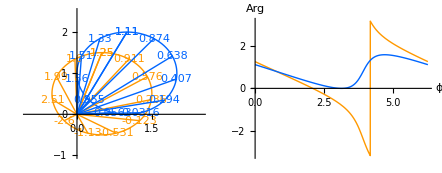

```mathematica
c1={0.5,0.5};c2={1.,1.};GraphicsRow[{Show[ParametricPlot[{c1+{Sin[t],Cos[t]},c2+{Sin[t],Cos[t]}},{t,0,2π},PlotStyle->{Hue[0.1],Hue[0.6]},AspectRatio->1,DisplayFunction->Identity,PlotRange->{{-1,2.5},{-1,2.5}}],Graphics[{Table[pt=c1+{Sin[t],Cos[t]};ang=ArcTan@@pt;{Hue[0.1],{Line[{{0,0},pt}]},{Text[NumberForm[ang,3],pt,Background->White]}},{t,0,2π,2π/11}],Table[pt=c2+{Sin[t],Cos[t]};ang=ArcTan@@pt;{Hue[0.6],{Line[{{0,0},pt}]},{Text[NumberForm[ang,3],pt,Background->White]}},{t,0,2π,2π/11}]}],DisplayFunction->$DisplayFunction],Plot[{ArcTan@@(c1+{Sin[t],Cos[t]}),ArcTan@@(c2+{Sin[t],Cos[t]})},{t,0,2π},PlotStyle->{Hue[0.1],Hue[0.6]},AxesLabel->{ϕ,Arg}]}]
```

As we move the around the curve, you notice for the blue curve that the phase (the number plotted on the line connecting to the point for which we calculate the phase) gently oscillates up and down, and thus the answer of the contour integral is  zero; for the orange curve we see a jump at the negative x-axis. This is due to a convention used in mathematica; in principle we can put this jump along any half-line in the complex plane ending at the origin.
If we move the value at the right of the jump down by 2π (making the function contnuous) we realise that the begin and endpoint differ in pahse by 2π. Thus for any contour enclosing the origin the phase changes by 2π, and thus we expect that

∮z^-1 ⅆz=±2πⅈ

for a contour enclosing the origin. The sign is positive if we integrate around in the positive sense (anti-clockwise), and negative if we do the integral along a contour that encircles the origin in a clockwise fashion.

If a function f(z) behaves like 1/(z-c) near the point c, we say that the function has a pole at z=c.

## 3. Residues

We are now ready to make the general statement:
If a function f(z) has a term R/(z-c) in its Laurent series around the point c (i.e., it is not analytic in a region around c, but it has an "isolated singularity" at c), then for any contour that encloses this and only this pole

∮f(z)ⅆz=±2πⅈ R

Here R is called the residue of f at c, and the sign depends on the orientation of the contour around c.

If multiple singularities are enclosed, we find that (all residues contribute with the same sign, since the contour must enclose them with the same orientation!)

∮f(z)ⅆz=±2πⅈ∑_k R_k

We can find the residue by expanding f(z) around c; it is often more useful (quicker) to look at the limit

lim_(z→c) (z-c)f(z)=R.

This works if there are no higher order singularities, i.e. no terms b_-2/(z-c)^2, etc. in the Laurent series.

## 4. Example 1: Simplest case

Contour integration is most commonly used to calculate integrals along the real axis, by turning them into complex integrals.

Calculate the integral

∫_(-∞)^∞ 1/(1+x^2)ⅆx

We actually know this one: it is [atan(x)]_(-∞)^∞=π. This is the simplest example of an integral doable by contour integration. Rewrite as a complex integral

∫_(-∞)^∞ 1/(1+z^2)ⅆz

As |z|→∞, the integral over the half circle z=R ⅇ^(ⅈ ϕ) (R fixed) gives (ⅆz=ⅆ(R ⅇ^(ⅈ ϕ))=R ⅇ^(ⅈ ϕ) ⅈ ⅆ ϕ)

∫_-R^R 1/(1+z^2)ⅆz=R ∫_0^π 1/(1+R^2 ⅇ^(2ⅈ ϕ))ⅆ ⅇ^(ⅈ ϕ)∝1/R→ 0.

This means we can close of the integral by adding a contour from ∞ to -∞ along a half circle. We easily see that z^2+1=(z+i)(z-i), and thus has poles in the upper and lower half plane. Only the one in the upper half plane is contained inside the contour, which goes around in positive sense.

The residue is

```mathematica
Residue[1/(z^2+1),{z,ⅈ}]
```

-ⅈ/2

and thus

∫_(-∞)^∞ 1/(1+x^2)ⅆx=∫_(-∞)^∞ 1/(1+z^2)ⅆz=∳1/(1+z^2)ⅆz=-ⅈ/22π ⅈ=π

as we know should be the case.

Note that in order to work, the ratio of denomiator over numerator should be at least 1/R^2 for large radius.

## 5. Example 2: Complex exponentials

The most common problem is with complex exponentials (or sines and cosines which can be written as such).

Calculate the integral (which falls slowly for large x!)

∫_(-∞)^∞ ⅇ^(ⅈ k x)/(ⅈ-x)ⅆx

We shall analyse this for k>0.

If we substitute x=z=R ⅇ^(ⅈ ϕ), we find

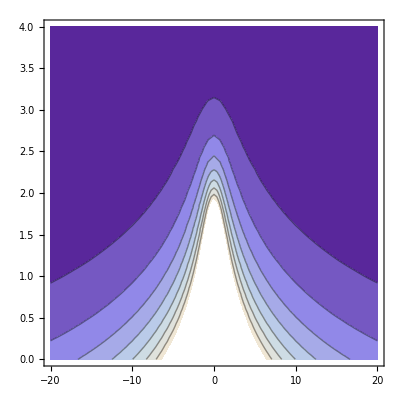

```mathematica
ContourPlot[Abs[ⅇ^(ⅈ (x+ⅈ y))/(ⅈ-(x+ⅈ y))],{x,-20,20},{y,0,4}]
```

The problem can be seen on substitution of z=R ⅇ^(ⅈ ϕ), for R  fixed (as a bove)

```mathematica
Simplify[ComplexExpand[ⅇ^(ⅈ k x)/(ⅈ-x)/.x-> R ⅇ^(ⅈ ϕ)]]
```

(ⅇ^(-k R sin(ϕ)) (cos(k R cos(ϕ))+ⅈ sin(k R cos(ϕ))))/(-R cos(ϕ)-ⅈ R sin(ϕ)+ⅈ)

For sin(ϕ)>0 the integrand goes to zero very quickly with R, but for ϕ=0 we enter a grey territory, where the integrand decays like 1/R. If we move the original integral up by just a little bit (ϵ) we are OK, since ϕ doesn't become zero. Thus

∫_(-∞)^∞ ⅇ^(ⅈ k x)/(ⅈ-x)ⅆx=∫_(-∞+ⅈ ϵ)^(∞+ⅈ ϵ) ⅇ^(ⅈ k z)/(ⅈ-z)ⅆz=∳ⅇ^(ⅈ k z)/(ⅈ-z)ⅆz

```mathematica
Residue[ⅇ^(ⅈ k z)/(ⅈ-z),{z,ⅈ}]
```

-ⅇ^-k

∫_(-∞)^∞ ⅇ^(ⅈ k x)/(ⅈ-x)ⅆx=∫_(-∞+ⅈ ϵ)^(∞+ⅈ ϵ) ⅇ^(ⅈ k z)/(ⅈ-z)ⅆz=∳ⅇ^(ⅈ k z)/(ⅈ-z)ⅆz=2π ⅈ (-ⅇ^-k)=-2π ⅈ  ⅇ^-k  (k>0)

In the same way we can show that for k<0 we must close the contour in the lower plane (since k sin(ϕ) must be negative)

∫_(-∞)^∞ ⅇ^(ⅈ k x)/(ⅈ-x)ⅆx=∫_(-∞-ⅈ ϵ)^(∞-ⅈ ϵ) ⅇ^(ⅈ k z)/(ⅈ-z)ⅆz=∲ⅇ^(ⅈ k z)/(ⅈ-z)ⅆz=-2π ⅈ (0)=0  (k<0)

since no pole is enclosed inside the contour.

## 6. Final case: poles on the real axis

The techniques shown above fail if a pole occurs on the real axis, since we don't know what side of the contour it lies! The technique to deal with that is usually based on physics:
Determine whether there are physical conditions that must be satisfied on the quantity you wish to evaluate. Decide whether these imply that a pole should contribute (which means we needd to move the contour just outside this pole) or whether it should not contribute (contour just on the inside of this pole). There are even cases where the logical choice is to assign half on the inside and half on the outside. Clearly, the mathematics decides